```mathematica
Clear["Global`*"]
Column@NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../mathematica_plot_options.nb"}]]
lenNode=5;
getData[lenNode_]:=Module[{time,displacement,velocity,modeshape,freq,omega,data,s},
data=Import[FileNameJoin[{NotebookDirectory[],"result"<>ToString[lenNode]<>".json"}]];
time="time"/.data;
displacement="displacement"/.data;
velocity="velocity"/.data;
modeshape="mode_shape"/.data;
freq="freq"/.data;
omega=Sqrt[freq];
(*superposition[t_]:=Module[{},Sum[modeshape[[i]]*(1-Cos[omega[[i]] t])/omega[[i]]^2,{i,1,Length[freq]}]];*)
s=10000;
Return@{
{Log[2π*#1],Log@#2}&@@@interpolateAndFourier[time[[s;;s+ 5000]],displacement[[s;;s+5000,Length[displacement[[1]]]-1]]],
Table[Table[{omega[[i]],modeshape[[j]][[i]]},{i,1,Length[omega]}],{j,1,Length[modeshape]}]
};
];
data=Table[{i,#1,#2}&@@@getData[i][[1]],{i,2,27}];
```

plot2Doption
plot3Doption
framelabel[xlabel_String,ylabel_String,size_:20]
axeslabel2D[xlabel_String,ylabel_String,size_:20]
axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20]
axeslabel[labels_List,size_: 20]
importData
jsonInfo
interpolateAndFourier[time_List,disp_List,timeSpan_List: {}]
interpolateAndFourierTr[timedisp_List,timeSpan_List: {}]
MyFourier[list_,n_]
MyInverseFourier[list_,n_]
MyDiscreteConvolve[f_,g_]
MyDiscreteConvolveUsingCn[FourierGF_]
Rv[q_]
Rs[q_]
W2dQdt[q_,w_]
Q2Roll[{a_,b_,c_,d_}]
Q2Pitch[{a_,b_,c_,d_}]
Q2Yaw[{a_,b_,c_,d_}]
getOmegaFromKandDepth
getTFromLandDepth

```mathematica
ListLinePlot3D[
data
,PlotRange->All
,Joined->True]
```

-Graphics3D-

plot2Doption
plot3Doption
framelabel[xlabel_String,ylabel_String,size_:20]
axeslabel2D[xlabel_String,ylabel_String,size_:20]
axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20]
axeslabel[labels_List,size_: 20]
importData
jsonInfo
interpolateAndFourier[time_List,disp_List,timeSpan_List: {}]
interpolateAndFourierTr[timedisp_List,timeSpan_List: {}]
MyFourier[list_,n_]
MyInverseFourier[list_,n_]
MyDiscreteConvolve[f_,g_]
MyDiscreteConvolveUsingCn[FourierGF_]
Rv[q_]
Rs[q_]
W2dQdt[q_,w_]
Q2Roll[{a_,b_,c_,d_}]
Q2Pitch[{a_,b_,c_,d_}]
Q2Yaw[{a_,b_,c_,d_}]
getOmegaFromKandDepth
getTFromLandDepth

{{0.999948,-0.0102036,0.000104118,-1.06243×10^-6,1.08411×10^-8,-1.10623×10^-10,1.12881×10^-12,-1.15185×10^-14,1.17535×10^-16,-1.19934×10^-18,1.22382×10^-20,-1.24879×10^-22,1.27428×10^-24,-1.30028×10^-26,1.32682×10^-28,-1.3539×10^-30,1.38153×10^-32,-1.40972×10^-34,1.43849×10^-36,-1.46785×10^-38,1.49781×10^-40,-1.52837×10^-42,1.55957×10^-44,-1.59139×10^-46,1.6073×10^-48},{0.000376873,0.036186,-0.0721542,0.106937,-0.139961,0.170686,-0.198606,0.223261,-0.244248,0.26122,-0.2739,0.282078,-0.285621,0.28447,-0.278644,0.268239,-0.253425,0.234448,-0.211617,0.185309,-0.155955,0.124039,-0.0900848,0.0546499,-0.018317},{0.00074734,0.0717936,-0.139635,0.198334,-0.24405,0.27379,-0.285605,0.278724,-0.253596,0.211866,-0.156267,0.0904376,-0.0186876,-0.0542859,0.123706,-0.185027,0.234236,-0.268111,0.284435,-0.282138,0.261371,-0.223493,0.170985,-0.107284,0.036559},{0.00110516,0.106257,-0.198075,0.260918,-0.285592,0.268489,-0.212109,0.124702,-0.019052,-0.0893846,0.184746,-0.253081,0.284395,-0.274106,0.223719,-0.140606,0.0369237,0.0721595,-0.170687,0.244245,-0.282074,0.27864,-0.234445,0.155954,-0.0546495},{0.00144427,0.139022,-0.243681,0.285576,-0.253917,0.156858,-0.0193973,-0.123059,0.23382,-0.284357,0.261653,-0.171557,0.0372737,0.10661,-0.223035,0.282014,-0.268355,0.185578,-0.0550028,-0.0897396,0.211368,-0.278556,0.273997,-0.198866,0.0725145},{0.00175899,0.169562,-0.273487,0.268708,-0.157125,-0.0169115,0.184226,-0.278315,0.261782,-0.141197,-0.0355097,0.198102,-0.281955,0.253737,-0.124666,-0.0539563,0.211133,-0.284389,0.244609,-0.107603,-0.0721723,0.223261,-0.28561,0.234436,-0.0900801},{0.00204407,0.197383,-0.285544,0.212741,-0.020015,-0.183994,0.284284,-0.224321,0.0379067,0.169876,-0.281899,0.235013,-0.0556482,-0.155085,0.278396,-0.244773,0.0731693,0.13968,-0.273791,0.253564,-0.0904006,-0.123722,0.268102,-0.26135,0.107274},{0.0022948,0.22203,-0.279048,0.125794,0.12225,-0.278175,0.224486,-0.00163915,-0.222442,0.278906,-0.125205,-0.122842,0.278324,-0.224079,0.000983496,0.222853,-0.278763,0.124615,0.123434,-0.278472,0.223672,-0.000327832,-0.223263,0.278618,-0.124025},{0.00250709,0.243097,-0.254398,0.0205028,0.233153,-0.26209,0.038417,0.222283,-0.268741,0.0561786,0.21053,-0.274324,0.0737171,0.197941,-0.278818,0.0909626,0.184565,-0.282204,0.107847,0.170456,-0.284468,0.124303,0.155669,-0.285603,0.140265},{0.00267753,0.260232,-0.213171,-0.0878054,0.284194,-0.14207,-0.169278,0.278993,-0.0563902,-0.233381,0.245164,0.0350756,-0.273536,0.186179,0.122942,-0.285623,0.108089,0.198193,-0.268401,0.0189071,0.253107,-0.223637,-0.0722144,0.282049,-0.155926},{0.00280344,0.273144,-0.158027,-0.183339,0.262216,0.0343243,-0.281723,0.125775,0.210246,-0.245255,-0.0708707,0.28553,-0.0913924,-0.233593,0.22414,0.106217,-0.284502,0.055462,0.252984,-0.199229,-0.139764,0.278656,-0.0185923,-0.26809,0.170944},{0.0028829,0.281606,-0.0925425,-0.252142,0.172821,0.197118,-0.235581,-0.122112,0.27446,0.0347278,-0.285517,0.0561769,0.267631,-0.141387,-0.222615,0.212265,0.155033,-0.261625,-0.0717349,0.284464,-0.0188347,-0.278468,0.107495,0.244243,-0.185259},{0.00291479,0.285465,-0.0209764,-0.284138,0.0389541,0.281674,-0.0567758,-0.278081,0.0743702,0.273376,-0.0916669,-0.267576,0.108597,0.260705,-0.125092,-0.25279,0.141086,0.243864,-0.156515,-0.233961,0.171318,0.223122,-0.185435,-0.211389,0.19881},{0.0028988,0.284641,0.0520001,-0.274612,-0.104965,0.254367,0.154025,-0.224661,-0.197355,0.186597,0.233344,-0.141591,-0.260653,0.0913193,0.278266,-0.0376501,-0.285527,-0.0174197,0.282167,0.0718415,-0.268311,-0.123591,0.244474,0.170743,-0.211543},{0.00283537,0.27913,0.12161,-0.224913,-0.221883,0.12599,0.278053,-0.00202528,-0.278956,-0.122342,0.224412,0.222392,-0.125263,-0.278238,0.00121517,0.27878,0.123074,-0.22391,-0.2229,0.124534,0.278421,-0.000405059,-0.278602,-0.123804,0.223406},{0.00272573,0.269006,0.183281,-0.142274,-0.281658,-0.0524817,0.245369,0.222145,-0.0917646,-0.285597,-0.105714,0.212499,0.252649,-0.0378022,-0.278788,-0.154969,0.171633,0.273646,0.0175827,-0.261489,-0.198392,0.124308,0.284346,0.072306,-0.23435},{0.00257184,0.254421,0.232953,-0.03877,-0.268843,-0.210106,0.0743425,0.278927,0.183868,-0.108715,-0.284508,-0.154662,0.141333,0.285498,0.122961,-0.17167,-0.281881,-0.0892746,0.199237,0.273714,0.0541477,-0.223588,-0.261129,-0.0181469,0.24433},{0.00237636,0.235603,0.26734,0.0704449,-0.186695,-0.284172,-0.138622,0.125479,0.282269,0.19766,-0.05599,-0.261757,-0.243666,-0.0171903,0.223987,0.273609,0.0892373,-0.171451,-0.285512,-0.155401,0.107611,0.278593,0.21132,-0.0366762,-0.253306},{0.00214258,0.212855,0.284158,0.169354,-0.0563677,-0.245172,-0.273402,-0.122569,0.10854,0.268561,0.25269,0.07132,-0.15676,-0.282171,-0.222775,-0.017474,0.199272,0.285506,0.184749,-0.0370082,-0.234527,-0.278444,-0.139995,0.0901428,0.261242},{0.00187438,0.186544,0.282277,0.243431,0.0885269,-0.108584,-0.253926,-0.278206,-0.169848,0.0194861,0.19953,0.284446,0.233749,0.0716099,-0.12467,-0.261513,-0.273676,-0.155361,0.0370237,0.211757,0.285533,0.223178,0.0544204,-0.140283,-0.268105},{0.00157615,0.157105,0.261798,0.281779,0.210582,0.071246,-0.091144,-0.224042,-0.284445,-0.252807,-0.139367,0.0191692,0.171503,0.268342,0.278351,0.198292,0.0540704,-0.107648,-0.234533,-0.285529,-0.244134,-0.123742,0.0366895,0.185249,0.273867},{0.00125273,0.125025,0.224054,0.278742,0.278264,0.222716,0.123091,-0.000894809,-0.124703,-0.223832,-0.278663,-0.278345,-0.22294,-0.123414,0.000536886,0.124381,0.22361,0.278584,0.278425,0.223163,0.123736,-0.000178962,-0.124059,-0.223387,-0.278505},{0.000909332,0.0908406,0.171524,0.234745,0.274067,0.285487,0.267843,0.222931,0.155323,0.0719019,-0.0188392,-0.107662,-0.185525,-0.2445,-0.278583,-0.284304,-0.261082,-0.211279,-0.139967,-0.0544057,0.0366948,0.12406,0.198794,0.25329,0.282},{0.000551451,0.0551248,0.107667,0.156241,0.199057,0.234538,0.261376,0.278582,0.285521,0.281939,0.267967,0.244119,0.211276,0.170647,0.123729,0.0722512,0.0181111,-0.0366964,-0.0901515,-0.140284,-0.185248,-0.223384,-0.253289,-0.273859,-0.284338},{0.000184797,0.0184789,0.0366971,0.0547647,0.0726074,0.090152,0.107326,0.12406,0.140285,0.155933,0.170941,0.185248,0.198793,0.211523,0.223384,0.234328,0.244309,0.253288,0.261227,0.268093,0.273858,0.278499,0.281997,0.284337,0.285509}}

{8.11257×10^10,3.23137×10^9,3.19159×10^9,3.12604×10^9,3.03577×10^9,2.92228×10^9,2.78743×10^9,2.63345×10^9,2.46287×10^9,2.27848×10^9,2.08333×10^9,1.88062×10^9,1.67367×10^9,1.4659×10^9,1.2607×10^9,1.06145×10^9,8.71422×10^8,6.93724×10^8,5.31275×10^8,3.86736×10^8,2.62478×10^8,1.60537×10^8,8.25829×10^7,2.9893×10^7,3.33055×10^6}

{284826.,56845.1,56494.2,55911.,55097.8,54058.1,52796.1,51317.2,49627.3,47733.4,45643.5,43366.1,40910.5,38287.1,35506.3,32579.9,29519.9,26338.6,23049.4,19665.6,16201.2,12670.3,9087.51,5467.45,1824.98}

10000

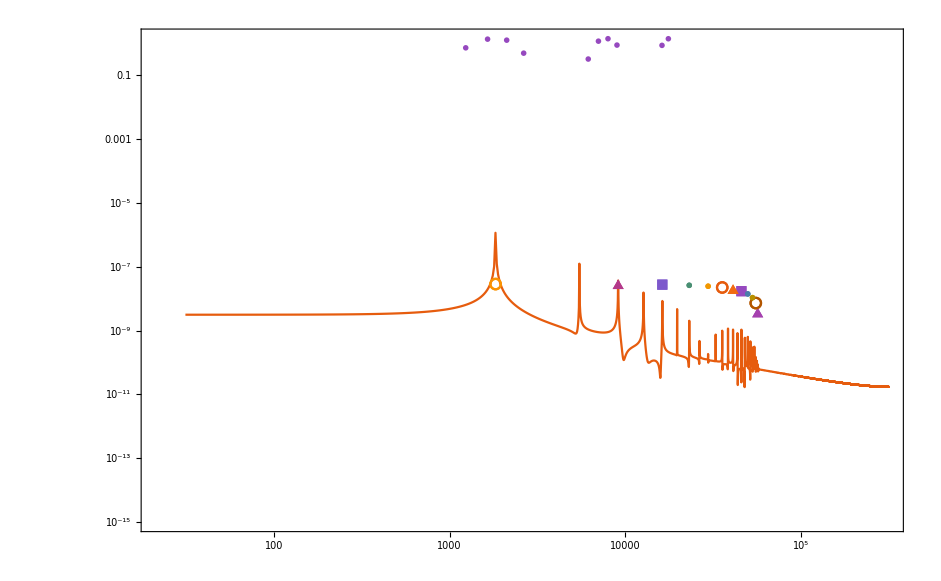

```mathematica
Clear["Global`*"]
Column@NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../mathematica_plot_options.nb"}]]

lenNode=25;
data=Import[FileNameJoin[{NotebookDirectory[],"result"<>ToString[lenNode]<>".json"}]];
time="time"/.data;
displacement="displacement"/.data;
velocity="velocity"/.data;
modeshape="mode_shape"/.data
freq="freq"/.data
omega=Sqrt[freq]
superposition[t_]:=Module[{},Sum[modeshape[[i]]*(1-Cos[omega[[i]] t])/omega[[i]]^2,{i,1,Length[freq]}]];

Animate[
ListPlot[Table[Transpose[{superposition[t][[i]],(i-1)/(lenNode-1)}],{i,1,lenNode}]
,PlotMarkers->Automatic
,PlotRange->{0.000001*{-1,1},{-0.1,1}}
,FrameLabel->{"x [m]","y [m]"}
,Evaluate[plot2Doption]
,PlotLabel->Style["StyleBox[\"T\",FontSlant->\"Italic\"]="<>ToString@displacement[[t,1]]]
,Joined->True
,AspectRatio->1.5]
,{t,1,Length[displacement],1}]

(*Animate[
ListPlot[Table[Transpose[{displacement[[t,i+1]],(i-1)/(lenNode-1)}],{i,1,lenNode}]
,PlotMarkers->Automatic
,PlotRange->{0.000001*{-1,1},{-0.1,1}}
,FrameLabel->{"x [m]","y [m]"}
,Evaluate[plot2Doption]
,PlotLabel->Style["StyleBox[\"T\",FontSlant->\"Italic\"]="<>ToString@displacement[[t,1]]]
,Joined->True
,AspectRatio->1.5]
,{t,1,Length[displacement],10}]*)


omegaContinuos={10.406861,65.218685,182.614206,357.850959,591.553276,883.678163,1234.228187,1643.203208,2110.603231,2636.428257,3220.678287,3863.353319,4564.453354,5323.978392,6141.928433,7018.303477,7953.103524,8946.328574,9997.978627,11108.053683,12276.553742,13503.478803,14788.828868,16132.603935,17534.804006};
amp=-{0.000000,0.418305,1.142648,1.510970,1.196085,0.302675,-0.724655,-1.354639,-1.259540,-0.493000,0.536586,1.281987,1.347192,0.697430,-0.322471,-1.171166,-1.398172,-0.882997,0.100890,1.031225,1.414169,1.046449,0.123257,-0.865362,-1.394633,-1.183609,-0.344306,0.677760,1.340060,1.291034,0.556705,-0.473131,-1.251823,-1.366024,-0.755119,0.256607,1.132111,1.406677,0.934570,-0.033447,-0.984375,-1.412109,-1.089844,-0.187500,0.812500,1.375000,1.187500,0.375000,-0.750000,-1.500000,-1.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000,0.000000};

s=10000
ListLogLogPlot[
Join[{{2π*#1,#2}&@@@interpolateAndFourier[time[[s;;s+ 20000]],displacement[[s;;s+20000,Length[displacement[[1]]]-1]]]},
Table[Table[{omega[[j]],modeshape[[j]][[-1]]*10^-7},{i,1,1}],{j,1,Length[omega]}],
{Table[{omegaContinuos[[i]],amp[[i]]},{i,1,Length[omegaContinuos]}]}]
,Joined->Join[{True},Table[False,{i,50}]]
,PlotMarkers->Join[{None},Table[Automatic,{i,50}]]
,PlotRange->{Automatic,{10^-15,Automatic}}
,Evaluate[plot2Doption]]
```

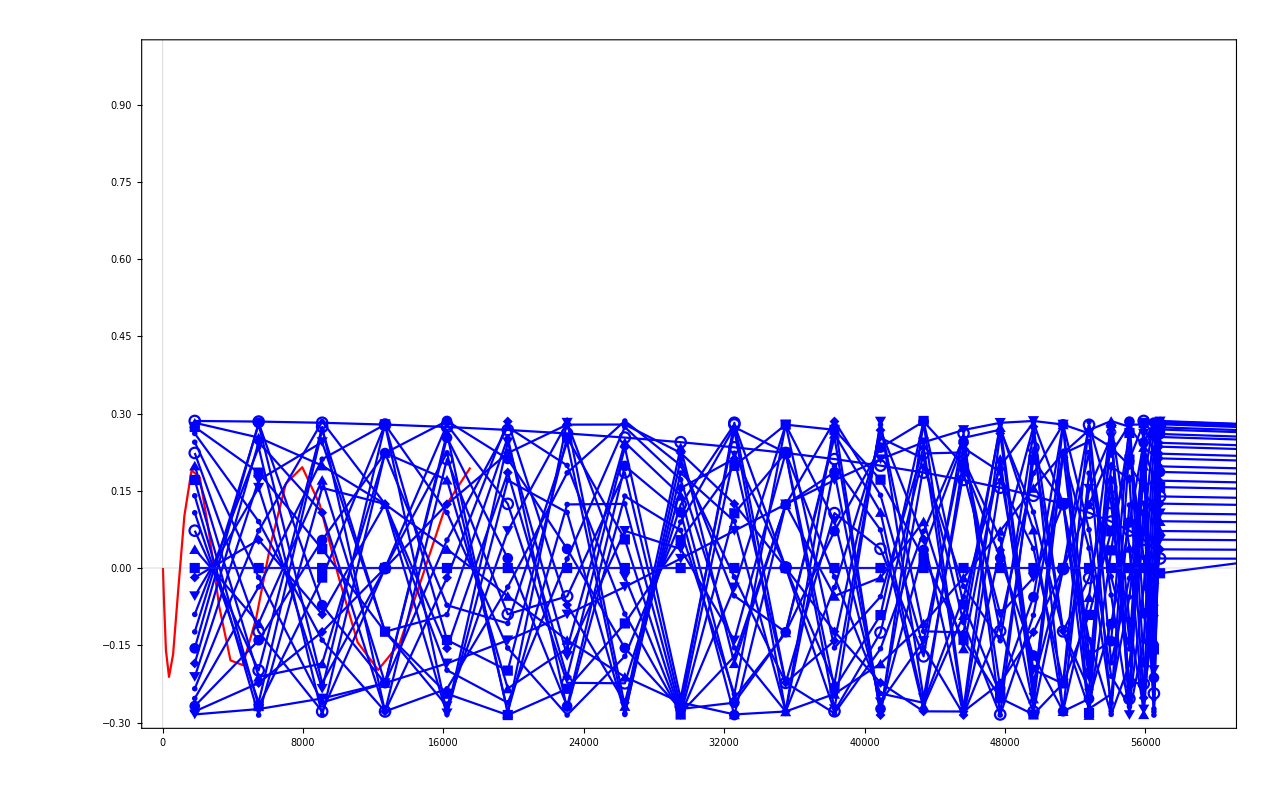

```mathematica
ListPlot[
Join[{Table[{omegaContinuos[[i]],amp[[i]]/Norm[amp]},{i,1,Length[omegaContinuos]}]},
Table[Table[{omega[[i]],modeshape[[j]][[i]]/Norm[modeshape[[j]]]},{i,1,Length[omega]}],{j,1,Length[modeshape]}]
]
,Joined->True
,PlotStyle->Join[{Red},Table[Blue,{i,50}]]
,PlotMarkers->Join[{None},Table[Automatic,{i,50}]]
,PlotRange->{{Automatic,60000},Automatic}
,Evaluate[plot2Doption]]
```

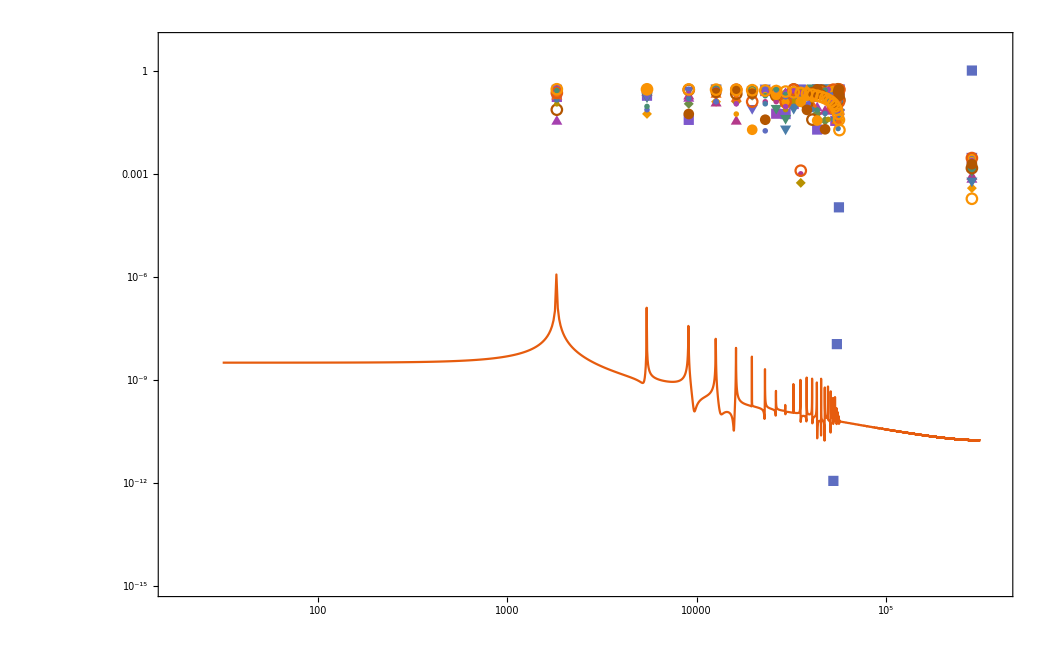

```mathematica
f=474.;
ω=2π*f

f=1406.;
ω=2π*f

f=2302.;
ω=2π*f
```

2978.23

8834.16

14463.9

```mathematica
0.118*2*1000*9.81*0.097
```

224.571

```mathematica
Import[FileNameJoin[{NotebookDirectory[],"result.txt"}]]
Graphics3D[Arrow[{#2,#1}]&@@@list,
PlotRange->{{-1,1},{-1,1},{-1,1}}]
```

Import::nffil: Importの最中にファイル/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_ODE/result.txtが見付かりませんでした．

$Failed

-Graphics3D-

-Graphics3D-